{{x→0.970821,y→0.00941499},{x→-0.454,y→-0.406729},{x→0.0611734+0.0979598 ⅈ,y→0.861635-0.15873 ⅈ},{x→0.0611734-0.0979598 ⅈ,y→0.861635+0.15873 ⅈ}}

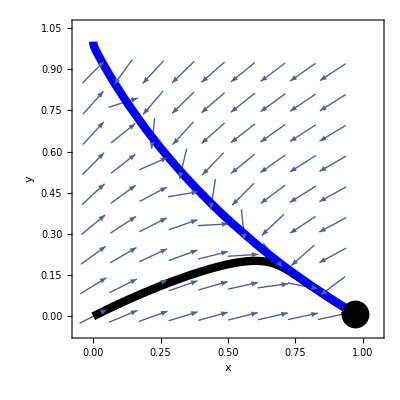

```mathematica
RR=2.1; BB=2;Aa = 2; Ab = 1;GG = 0.1;
f[x_,y_]=(1-x-y)*(Aa+BB*Aa*x)-GG*x - RR*x*y;
g[x_,y_]=(1-x-y)*(Ab+BB*Ab*y)-GG*y - RR*x*y;
vp=VectorPlot[{f[x,y],g[x,y]},{x,0,1},{y,0,1},VectorScale->{0.08,1,None},Axes->True,AxesLabel->{x,y},VectorPoints->10,VectorColorFunction->Hue[0,0,1]];
cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,0,1},{y,0,1}];
ptRules1=NSolve[{f[x,y]==0,g[x,y]==0},{x,y}]
sol[{x0_,y0_,tmin_,tmax_}]:=NDSolveValue[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tmin,tmax}]; 
sep=ParametricPlot[Evaluate@sol[{0,1,0,100}],{t,0,100},PlotStyle->{Blue,Thickness[.015]},PlotLabel->"Stable Manifold"];
trac1=ParametricPlot[Evaluate@sol[{0,0,0,100}],{t,0,100},PlotStyle->{Black,Thickness[.015]}];
Show[vp,trac1,sep,Graphics[{Black,PointSize[0.05],Point[{x,y}]/.ptRules1[[1]]}],LabelStyle->Directive[Black,Large]]
```